```mathematica
(*改入射光线作图可以只保留螺旋线在边界内部分，已成功*)
q={};(*PSOS点数据*)
Table[
Clear[a,z0,p,a2,a3,b2,b3,p1,R1,R2,R0,θ,u1,x00,y00,z00];
p={};(*螺线图*)
(*q={};(*PSOS点数据*)*)
a=j;(*螺旋线速率*)
a2=-0.1329;a3=0.0948;
b2=-0.0642;b3=-0.0224;(*face腔左右参数*)
(*a2=0.;a3=0;
b2=0;b3=0;(*正圆腔左右参数*)*)

z0=1.;(*卷曲圆柱半径*)
R0=1;(*face腔基础半径*)
R1=R0*(1+a2*Cos[θ]^2+a3*Cos[θ]^3);
R2=R0*(1+b2*Cos[θ]^2+b3*Cos[θ]^3);
{x00,y00,z00}={R2*Cos[θ],z0*Sin[R2*Sin[θ]/z0],-z0*Cos[R2*Sin[θ]/z0]}/.θ->π;(*起始点*)

{Rx1,Ry1,Rz1}=D[{R1*Cos[θ],z0*Sin[R1*Sin[θ]/z0],-z0*Cos[R1*Sin[θ]/z0]},θ];{Rx2,Ry2,Rz2}=D[{R2*Cos[θ],z0*Sin[R2*Sin[θ]/z0],-z0*Cos[R2*Sin[θ]/z0]},θ];(*边界切向量*)
u0=Sign[z00]*ArcCos[y00/z0];


p1=ParametricPlot3D[{{R1*Cos[θ],z0*Sin[R1*Sin[θ]/z0],-z0*Cos[R1*Sin[θ]/z0]},{R2*Cos[θ],z0*Sin[R2*Sin[θ]/z0],-z0*Cos[R2*Sin[θ]/z0]}},{θ,-π,π},PlotStyle->{AxesLabel->{}}(*,PlotRange->{{-1.2R0,1.2R0}}*)];
(*卷曲Face腔边界*)
findpoint[R_]:={{mm,nn}=(Solve[x*Cos[θ]==a*u+x00&&x*Sin[θ]/z0==u+u0+π/2&&-π<θ<=π+0.0001,{θ,u},Reals])/.(x->If[R==R1,R2,R1]);min=Min[m[[2]][[2]],n[[2]][[2]],mm[[2]][[2]],nn[[2]][[2]]];max=Max[m[[2]][[2]],n[[2]][[2]],mm[[2]][[2]],nn[[2]][[2]]];p2=ParametricPlot3D[{a*(θ)+x00,z0*Cos[θ+u0],z0*Sin[θ+u0]},{θ,min,max},PlotStyle->{Thickness[0.002],Black},(*PlotRange->{-1.2*R0,1.2*R0}*)PlotPoints->50];};
Table[
u0=Sign[z00]*ArcCos[y00/z0];(*起始点在螺旋线上相位，用于确定螺旋线位置*)
{m,n}=Solve[R0*Cos[θ]==a*u+x00&&R0*Sin[θ]/z0==u+u0+π/2&&-π<θ<=π,{θ,u},Reals];(*用螺旋线与R0半径的标准圆的交点x坐标确定Face腔参数*)
m1={R2*Cos[θ],z0*Sin[R2*Sin[θ]/z0],-z0*Cos[R2*Sin[θ]/z0]}/.m[[1]];n1={R2*Cos[θ],z0*Sin[R2*Sin[θ]/z0],-z0*Cos[R2*Sin[θ]/z0]}/.n[[1]];
{x11,y11,z11}=If[Norm[m1-{x00,y00,z00}]>Norm[n1-{x00,y00,z00}],m1,n1];(*选出标准圆上第二点坐标*)
{Rx,Ry,Rz,R}=If[x11>=0,{Rx1,Ry1,Rz1,R1},{Rx2,Ry2,Rz2,R2}];

(*ua=a^2+z0^2;ub=2*(x00*a+z0^2*(u0+π/2));uc=x00^2+z0^2*(u0+π/2)^2-R0^2;
uu1=(-ub+Sqrt[ub^2-4*ua*uc])/(2*ua);uu2=(-ub-Sqrt[ub^2-4*ua*uc])/(2*ua)
R=If[>=0,R1,R2];*)
(*R=R2;*)
(*u0=Sign[z00]*ArcCos[y00/z0];(*起始点在螺旋线上相位，用于确定螺旋线位置*)*)
(*Print[R];*)
(*o=NSolve[R*Cos[θ]==a*u+x00&&R*Sin[θ]/z0==u+u0+π/2&&-π<θ<π,{θ,u},Reals];
If[Length[o]≠2,Print["lessthan2"],Print["yes"]];*)
{m,n}=Solve[R*Cos[θ]==a*u+x00&&R*Sin[θ]/z0==u+u0+π/2&&-π<θ<=π+0.000000000001,{θ,u},Reals,WorkingPrecision->10];

(*求螺旋线与边界交点，腔边界与螺旋线分别是θ,u的参数方程，联立三个坐标相等化简得这两个方程组，原方程参数形式见p11,p1*)
(*θ取0-2π时solve和nsolve容易只求出一对θ,u解，改为-π~π就好了*)

(*p2=ParametricPlot3D[{a*(θ)+x00,z0*Cos[θ+u0],z0*Sin[θ+u0]},{θ,u/.m[[2]],u/.n[[2]]},PlotStyle->{Thickness[0.001],Black},PlotRange->{-1.2*R0,1.2*R0}];(*用入射光线作螺线图*)*)
m1={R*Cos[θ],z0*Sin[R*Sin[θ]/z0],-z0*Cos[R*Sin[θ]/z0]}/.m[[1]];n1={R*Cos[θ],z0*Sin[R*Sin[θ]/z0],-z0*Cos[R*Sin[θ]/z0]}/.n[[1]];
(*Print[m1,n1];*)
m1={R*Cos[θ],z0*Sin[R*Sin[θ]/z0],-z0*Cos[R*Sin[θ]/z0]}/.m[[1]];n1={R*Cos[θ],z0*Sin[R*Sin[θ]/z0],-z0*Cos[R*Sin[θ]/z0]}/.n[[1]];
If[m1[[1]]*n1[[1]]<0,findpoint[R],p2=ParametricPlot3D[{a*(θ)+x00,z0*Cos[θ+u0],z0*Sin[θ+u0]},{θ,u/.m[[2]],u/.n[[2]]},PlotStyle->{Thickness[0.002],Black},(*PlotRange->{-1.2*R0,1.2*R0}*)PlotPoints->50];(*用入射光线作螺线图*)];

f=If[Norm[m1-{x00,y00,z00}]>Norm[n1-{x00,y00,z00}],m[[1]],n[[1]]];(*选出第二点θ值*)
{x11,y11,z11}=If[Norm[m1-{x00,y00,z00}]>Norm[n1-{x00,y00,z00}],m1,n1];(*选出第二点坐标*)
u1=Sign[z11]*ArcCos[y11/z0];(*第二点螺旋线参数相位，用于作第二点螺旋线*)
t1=D[{a*(θ)+x11,z0*Cos[θ+u1],z0*Sin[θ+u1]},θ];t1=t1/.θ->0;t1=t1/Norm[t1];(*入射螺旋线上入射点切向量*)
nn={Rx,Ry,Rz}/.f;nn=nn/Norm[nn];(*边界法向量*)
{m1,n1}=Solve[t1.nn=={x,y,z}.nn&&Norm[{x,y,z}]==1&&{x,y,z}.{0,y11,z11}==0,{x,y,z},Reals];(*应用反射定律求出射向量*)
t=If[({x,y,z}/.n1).t1>({x,y,z}/.m1).t1,m1,n1];(*反射向量*)
tt={x,y,z}/.t;tt=If[tt[[1]]>=0,tt,-tt];(*将反射向量统一到x正方向，用于确定反射螺旋速率正负号*)
a1=Sign[Cross[{0,y11,z11},{0,tt[[2]],tt[[3]]}][[1]]]*(tt[[1]])*z0/Sqrt[(tt[[2]])^2+(tt[[3]])^2];(*反射螺旋速率，由反射向量直接计算的出*)
(*p2=ParametricPlot3D[θ*({x,y,z}/.t)+{x11,y11,z11},{θ,-π,π},PlotStyle->{Thickness[0.001],Black},PlotRange->{-2R0,2R0}];*)
(*p2=ParametricPlot3D[{a*(θ)+x00,z0*Cos[θ+u0],z0*Sin[θ+u0]},{θ,-π,π},PlotStyle->{Thickness[0.001],Black},PlotRange->{-1.2*R0,1.2*R0}];*)
p=Append[p,p2];
q1={If[(θ/.f)≥0,θ/.f,(θ/.f) +2π]/(2π),Abs[Cos[VectorAngle[tt,nn]]]};
q=Append[q,q1];
{x00,y00,z00}={x11,y11,z11};(*更新初始点*)
a=a1;(*更新螺旋线速率*)

{}
,{i,1,50}],{j,{0.6}}];//AbsoluteTiming

Show[p1,p(*,p11*),AxesLabel->{Style[x],y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

General::stop: Further output of Solve::inex will be suppressed during this calculation.

{67.1543,Null}

-Graphics3D-

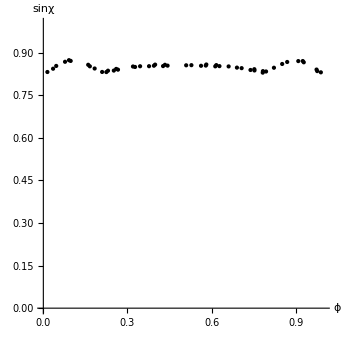

```mathematica
q=q;
(*qq=Append[qq,q];*)
ListPlot[q,AspectRatio->1, PlotStyle->{Black,PointSize[Small]},PlotRange->{{0,1},{0,1}},AxesLabel->{Style["ϕ",15],Style["sinχ",15]}]
```